## Cálculo de las secciones transversales empleando el modelo Drude-Lorentz y corrección de tamaño

En este Notebook se emplean las definiciones del modelo de Drude-Lorentz de Rakic en https://doi.org/10.1364/ao.37.005271
- Para el modelo de Drude se emplea
ϵ_Drude=1-(f_0 ω_p^2)/(ω (ω - i γ_0))
- Para el modelo de Lorentz se emplea
ϵ_Lorentz=∑_(j=1)^k 1+(f_j ω_p^2)/(ω_j^2-ω^2-iγω)
de tal forma que se obtiene

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
vlight=3*^17 ;(*nm s^-1*)
```

```mathematica
fjAu=List[0.760,0.024,0.010,0.071,0.601,4.384];
gammaAu=List[0.053,0.241,0.345,0.870,2.494,2.214];
omegaAu=List[0,0.415,0.830,0.969,4.304,13.32];
```

```mathematica
ϵDrude[ω_,ωp_,gamma_]:=1-(ωp^2/((ω)(ω+ I * gamma[[1]])));(*recibe en eV*)
ϵLorentz[ω_,ωp_,j_,fj_,omega_,gamma_]:=Sum[((fj[[i]]*(ωp)^2)/(((omega[[i]])^2-(ω)^2)-I * (ω)(gamma[[i]]))),{i,2,j}];
```

```mathematica
ϵ0Tot[ω_,ωp_,j_,fj_,omega_,gamma_]:=ϵDrude[ω,ωp,gammaAu]+ϵLorentz[ω,ωp,j,fjAu,omegaAu,gammaAu];(*recibe en eV*)
```

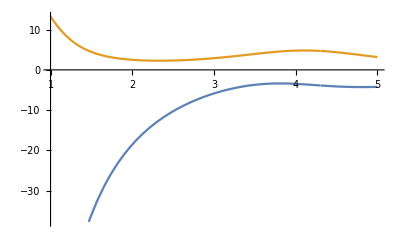

```mathematica
Plot[{Re[ϵ0Tot[ℏω,9.03,5,fjAu,omegaAu,gammaAu]],Im[ϵ0Tot[ℏω,9.03,5,fjAu,omegaAu,gammaAu]]},{ℏω,1,5}]
```

```mathematica
elipsoblato[a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1,L2,L3},
							L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L2=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L3=1-2 L1;
{L1,L2,L3}]
```

```mathematica
elipsprolato[a_,b_,c_]:=Module[{eab2=1-(b^2/a^2),L1,L2,L3},
							L1=((1-eab2)/eab2) (-1+((1/(2*Sqrt[eab2]))* Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]));
							L2=0.5*(1-L1);
							L3=0.5*(1-L1);{L1,L2,L3}];
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[a,b,c][[j]],
							b==c ,elipsprolato[a,b,c][[j]]]
```

```mathematica
Cabs[a_,b_,c_,nm_,λ_,λp_,j_,fj_,omega_,gamma_]:=Module[{ϵDrude,ϵLorentz,ϵTot,ϵm,k,αx,αz,Cabs},
										ϵm=nm^2;
										k=(2 Pi nm/λ);ϵDrude=1-((fj[[1]]*(2 Pi vlight/λp)^2)/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I * (gamma[[1]]/ℏ))));
								ϵLorentz=Sum[((fj[[i]]*(2 Pi vlight/λp)^2)/(((omega[[i]]/ℏ)^2-(2 Pi vlight/λ)^2)- I * (2 Pi vlight/λ)(gamma[[i]]/ℏ))),{i,2,j}];
										ϵTot=ϵDrude+ϵLorentz;
										αx=4 π a b^2  ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b^2 ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										Cabs=k Im[2 αx+αz]/3]
```

```mathematica
Csca[a_,b_,c_,nm_,λ_,λp_,j_,fj_,omega_,gamma_]:=Module[{ϵDrude,ϵLorentz,ϵTot,ϵm,k,αx,αz,Csca},
										ϵm=nm^2;
										k=(2 Pi nm/λ);ϵDrude=1-((fj[[1]]*(2 Pi vlight/λp)^2)/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I * (gamma[[1]]/ℏ))));
								ϵLorentz=Sum[((fj[[i]]*(2 Pi vlight/λp)^2)/(((omega[[i]]/ℏ)^2-(2 Pi vlight/λ)^2)- I * (2 Pi vlight/λ)(gamma[[i]]/ℏ))),{i,2,j}];
										ϵTot=ϵDrude+ϵLorentz;
										αx=4 π a b^2  ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵTot-ϵm)));
										αz=4 π a b^2 ((ϵTot-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵTot-ϵm)));
										Csca=k^4 Norm[2 αx+αz]^2/(18 Pi)]
```

```mathematica
Csca[1.5,1.5,1.0,1.33,500,h vlight/(9.083),2,fjAu,omegaAu,gammaAu]
Cabs[1.5,1.5,1.0,1.33,500,h vlight/(9.083),2,fjAu,omegaAu,gammaAu]
```

0.000111253

0.041151

```mathematica
Cext[a_,b_,c_,nm_,λ_,λp_,j_,fj_,omega_,gamma_]:=Csca[a,b,c,nm,λ,λp,j,fj,omega,gamma]+Cabs[a,b,c,nm,λ,λp,j,fj,omega,gamma];
```

```mathematica
Cext[1.5,1.5,1.0,1.33,500,h vlight/(9.083),6,fjAu,omegaAu,gammaAu]
```

1.53868

```mathematica
qextAu0=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(9.083),1,fjAu,omegaAu,gammaAu]},{λ,195,1937}];
qextAu1=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(9.083),2,fjAu,omegaAu,gammaAu]},{λ,195,1937}];
qextAu2=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(9.083),3,fjAu,omegaAu,gammaAu]},{λ,195,1937}];
qextAu3=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(9.083),4,fjAu,omegaAu,gammaAu]},{λ,195,1937}];
qextAu4=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(9.083),5,fjAu,omegaAu,gammaAu]},{λ,195,1937}];
qextAu5=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(9.083),6,fjAu,omegaAu,gammaAu]},{λ,195,1937}];
```

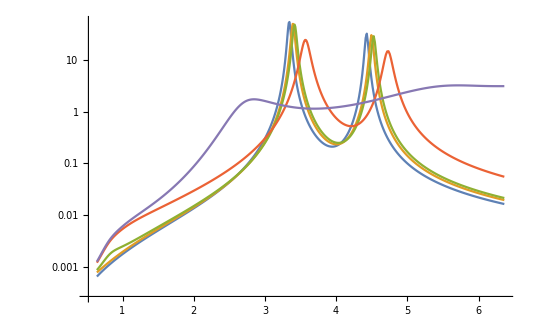

```mathematica
ListLinePlot[{qextAu0,qextAu1,qextAu2,qextAu3,qextAu4},PlotRange->All, ScalingFunctions->"Log"]
```

```mathematica
fjBi=List[0.9541,0.2573,0.1291,0.2559,0.184,0.4064];
gammaBi=List[0.09889,1.896,0.0011,1.155,0.001,3.472];
omegaBi=List[0,3.877,0.1,6.419,10.62,12.39];
```

```mathematica
qextBi0=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(10),1,fjBi,omegaBi,gammaBi]},{λ,100,1937}];
qextBi1=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(10),2,fjBi,omegaBi,gammaBi]},{λ,100,1937}];
qextBi2=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(10),3,fjBi,omegaBi,gammaBi]},{λ,100,1937}];
qextBi3=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(10),4,fjBi,omegaBi,gammaBi]},{λ,100,1937}];
qextBi4=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(10),5,fjBi,omegaBi,gammaBi]},{λ,100,1937}];
qextBi5=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(10),6,fjBi,omegaBi,gammaBi]},{λ,100,1937}];
```

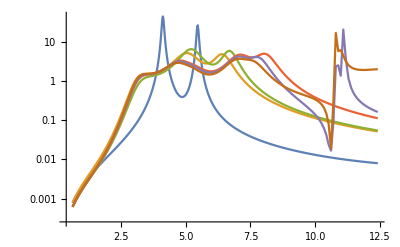

```mathematica
ListLinePlot[{qextBi0,qextBi1,qextBi2,qextBi3,qextBi4,qextBi5},PlotRange->All,ScalingFunctions->"Log"]
```